```mathematica
Clear["Global`*"]
```

```mathematica
(*Reward structure for player a (initial, CC, CD, DC, DD)*)
Rmat ={0,R,S,T,P};
(*Transition matrix (P_ij = prob. of going from i to j)*)
Pmat = {{0,a0*b0,a0*(1-b0),(1-a0)*b0,(1-a0)*(1-b0)},{0,a1*b1,a1*(1-b1),(1-a1)*b1,(1-a1)*(1-b1)},{0,a2*b2,a2*(1-b2),(1-a2)*b2,(1-a2)*(1-b2)},{0,a3*b3,a3*(1-b3),(1-a3)*b3,(1-a3)*(1-b3)},{0,a4*b4,a4*(1-b4),(1-a4)*b4,(1-a4)*(1-b4)}};
(*Direction solution of the Bellman equation*)
V=Inverse[IdentityMatrix[5] - gamma*Pmat].Rmat;
```

```mathematica
(*Series expansion of the solution*)
Series[V,{gamma,0,1}]
```

{(P-a0 P-b0 P+a0 b0 P+a0 b0 R+a0 S-a0 b0 S+b0 T-a0 b0 T) gamma+O[gamma]^2,R+(P-a1 P-b1 P+a1 b1 P+a1 b1 R+a1 S-a1 b1 S+b1 T-a1 b1 T) gamma+O[gamma]^2,S+(P-a2 P-b2 P+a2 b2 P+a2 b2 R+a2 S-a2 b2 S+b2 T-a2 b2 T) gamma+O[gamma]^2,T+(P-a3 P-b3 P+a3 b3 P+a3 b3 R+a3 S-a3 b3 S+b3 T-a3 b3 T) gamma+O[gamma]^2,P+(P-a4 P-b4 P+a4 b4 P+a4 b4 R+a4 S-a4 b4 S+b4 T-a4 b4 T) gamma+O[gamma]^2}

```mathematica
(*Reward structure for player b (initial, CC, CD, DC, DD)*)
Rmat2 ={0,R,T,S,P};
(*Direction solution of the Bellman equation*)
V2=Inverse[IdentityMatrix[5] - gamma2*Pmat].Rmat2;
```

```mathematica
(*Gradients -----------------------------------------------------------------------------------------------------------------------------------*)
(*DVa0total = InputForm[D[Total[V],a0]];*)
dVa0 = D[Total[V],a0];dVa1 = D[Total[V],a1];dVa2= D[Total[V],a2];dVa3 = D[Total[V],a3];dVa4 = D[Total[V],a4];
dVb0 = D[Total[V],b0];dVb1 = D[Total[V],b1];dVb2= D[Total[V],b2];dVb3 = D[Total[V],b3];dVb4 = D[Total[V],b4];

dV2b0 = D[Total[V2],b0];dV2b1 = D[Total[V2],b1];dV2b2= D[Total[V2],b2];dV2b3 = D[Total[V2],b3];dV2b4 = D[Total[V2],b4];

(*Hessian*)
dVdab = D[Total[V],{{a0,a1,a2,a3,a4,b0,b1,b2,b3,b4},2}];
(*2nd term in (4.4) w/o learning rates*)
LOLA = dVdab[[1;;5,6;;10]].{dV2b0,dV2b1,dV2b2,dV2b3,dV2b4};
Dimensions[LOLA]
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVa0_total.txt",{dVa0}];
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVa1_total.txt",{dVa1}];
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVa2_total.txt",{dVa2}];
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVa3_total.txt",{dVa3}];
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVa4_total.txt",{dVa4}];

Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVb0_total.txt",{dVb0}];
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVb1_total.txt",{dVb1}];
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVb2_total.txt",{dVb2}];
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVb3_total.txt",{dVb3}];
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVb4_total.txt",{dVb4}];

Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\LOLA_total.txt",LOLA, "CSV"];
```

{5}

```mathematica
Series[LOLA,{gamma2,0,2}]
```

{1,3,1}
 |  |  |  |

```mathematica
LOLA
```

{1,3,(-(((-gamma+a0 gamma+gamma^2-a0 gamma^2-a0 a1 gamma^2+a2 gamma^2-a3 gamma^2+43+a0 a1 b2 gamma^4-a1 a2 b2 gamma^4-a0 a3 b2 gamma^4+a2 a3 b2 gamma^4-a0 a1 b3 gamma^4+a0 a2 b3 gamma^4+a1 a3 b3 gamma^4-a2 a3 b3 gamma^4) (1) P)/(1-gamma-a2 gamma+156+a2 a3 b3 b4 gamma^4+a1 a4 b3 b4 gamma^4-a2 a4 b3 b4 gamma^4)^2)-((1) (1) R)/(1)^2+6+((gamma^2-a0 gamma^2-gamma^3+18+a2 b4 gamma^4) T)/(1-gamma-a2 gamma+157+a1 a4 b3 b4 gamma^4-a2 a4 b3 b4 gamma^4)) (1)+3+1}
 |  |  |  |

```mathematica
(*ZD-strategy -----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
p[chi_,phi_] := {1-2*phi*(chi-1),1-phi*(4*chi+1),phi*(chi+4),0}
```

```mathematica
p[3,1/26] (*Standard at midpoint chi)*)
p[3,2/26]
p[3,1/52]
```

{11/13,1/2,7/26,0}

{9/13,0,7/13,0}

{12/13,3/4,7/52,0}

```mathematica
(*dV1/da_0(gamma) -------------------------------------------------------------------------------------------------------------------------------*)
```

{gamma→0.770889}

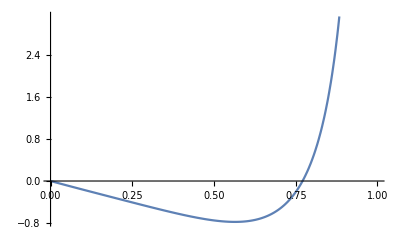

```mathematica
(*Initial: a, versus ZD-strat with extortion factor 3*)
Clear[a0,a1,a2,a3,a4,gamma];
R=3;S=0;T=5;P=1;
a=1;
a0 = a;a1=a;a2=a;a3=a;a4=a;
b0=0; b1=11/13;b2=7/26;b3=1/2;b4=0;
b0=0; b1=9/13;b2=7/13;b3=0;b4=0;
Clear[a1];
Va0 = D[Total[V],a1];
a1=9/13;
FindRoot[Va0,{gamma,0.8}]
Plot[Va0,{gamma,0,1}]
```

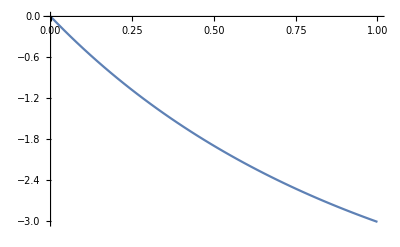

```mathematica
(*Initial: random, versus random*)
Clear[a0,a1,a2,a3,a4,gamma];
R=3;S=0;T=5;P=1;
a3=RandomReal[];a1=RandomReal[];a2=RandomReal[];a4=RandomReal[];
b0=RandomReal[]; b1=RandomReal[];b2=RandomReal[];b3=RandomReal[];b4=RandomReal[];
Va0 = D[Total[V],a0];
(*FindRoot[Va0,{gamma,0.5}]*)
Plot[Va0,{gamma,0,1}]
```

{gamma→1.}

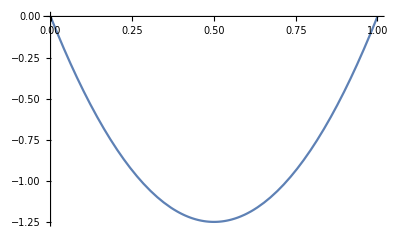

```mathematica
(*Initial: a, versus Tit-for-Tat*)
Clear[a0,a1,a2,a3,a4,gamma];
R=3;S=0;T=5;P=1;
a=1;
a0 = a;a1=a;a2=a;a3=a;a4=a;
b0=1; b1=1;b2=1;b3=0;b4=0;
Clear[a4];
Va0 = D[Total[V],a4];
a4=a;
FindRoot[Va0,{gamma,0.6}]
Plot[Va0,{gamma,0,1}]
```

{gamma→1.77878×10^-22}

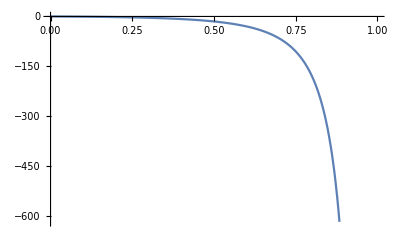

```mathematica
(*Initial: a; versus win-stay-lose-shift (Pavlov)*)
Clear[a0,a1,a2,a3,a4,gamma];
R=3;S=0;T=5;P=1;
a=1;
a0=a;a1=a; a2=a;a3=a;a4=a;
b0=1; b1=1;b2=0;b3=0;b4=1;
Clear[a2];
Va0 = D[Total[V],a2];
a2=a;
FindRoot[Va0,{gamma,0.5}]
Plot[Va0,{gamma,0,1}]
```

{gamma→0.5}

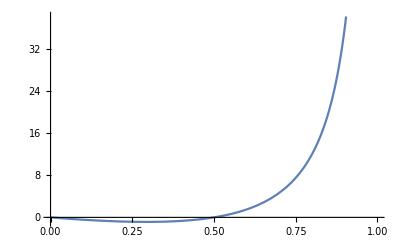

```mathematica
(*Initial: all-coop; versus win-stay-lose-shift (Pavlov)*)
Clear[a0,a1,a2,a3,a4,gamma];
R=3;S=0;T=5;P=1;
a1=1;a2=1;a3=1;a4=1;
b0=1; b1=1;b2=0;b3=0;b4=1;
Va0 = D[V,a0];
FindRoot[Va0[[1]],{gamma,0.5}]
Plot[Va0[[1]],{gamma,0,1}]
```

```mathematica
(*Initial: random, versus win-stay-lose-shift (Pavlov)*)
R=3;S=0;T=5;P=1;
a1=0.5;a2=0.5;a3=0.5;a4=0.5;
b0=1; b1=1;b2=0;b3=0;b4=1;
Va0 = D[V,a0];
FindRoot[Va0[[1]],{gamma,0.6}]
Plot[Va0[[1]],{gamma,0,1}]
```

{gamma→1.}

-Graphics-

{(5 (-gamma+gamma^2))/(1-gamma^2)+(3 (gamma-gamma^3))/(1-gamma^2)+(-gamma^2+gamma^3)/(1-gamma^2),0,0,0,0}

{gamma→1.}

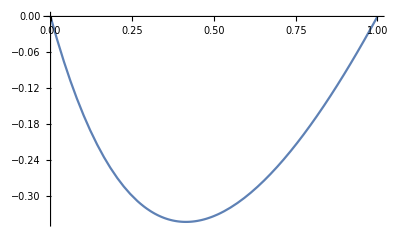

```mathematica
(*Initial: all-defect, versus win-stay-lose-shift (Pavlov)*)
R=3;S=0;T=5;P=1;
a1=0;a2=0;a3=0;a4=0;
b0=1; b1=1;b2=0;b3=0;b4=1;
Va0 = D[V,a0]
FindRoot[Va0[[1]],{gamma,0.5}]
Plot[Va0[[1]],{gamma,0,1}]
```

```mathematica
(*Vj(a_i) for tit-for-tat ------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*Initial: all-coop, versus Tit-for-Tat*)
R=3;S=0;T=5;P=1;
a = 1
b0=1; b1=1;b2=1;b3=0;b4=0;
gamma=1/3;
(*gamma = 2/3;*)
(*gamma = 1/3;*)
Simplify[V]
```

1

{3/2,9/2,3/2,11/2,3/2}

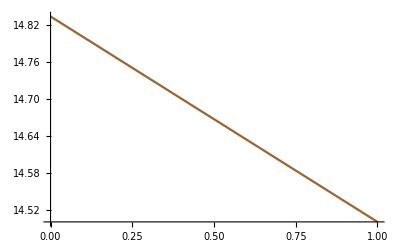

```mathematica
(*a0*)
Clear[a0]
a1=a;a2=a;a3=a;a4=a;
pltV1a0 = Plot[V[[1]],{a0,0,1},PlotStyle->Red];
pltV2a0 = Plot[V[[2]],{a0,0,1},PlotStyle->Green];
pltV3a0 = Plot[V[[3]],{a0,0,1},PlotStyle->Blue];
pltV4a0 = Plot[V[[4]],{a0,0,1},PlotStyle->Black];
pltV5a0 = Plot[V[[5]],{a0,0,1},PlotStyle->Yellow];
pltVsum = Plot[Total[V],{a0,0,1},PlotStyle->Brown];
(*Show[pltV1a0,pltV2a0,pltV3a0,pltV4a0,pltV5a0,pltVsum,PlotRange->All]*)
Show[pltVsum,PlotRange->All]
```

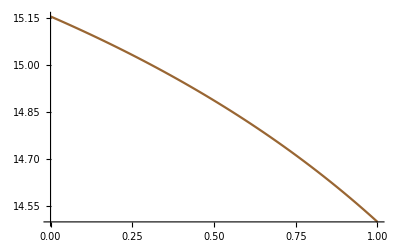

```mathematica
(*a1*)
Clear[a1]
a0=a;a2=a;a3=a;a4=a;
pltV1a1 = Plot[V[[1]],{a1,0,1},PlotStyle->Red];
pltV2a1 = Plot[V[[2]],{a1,0,1},PlotStyle->Green];
pltV3a1 = Plot[V[[3]],{a1,0,1},PlotStyle->Blue];
pltV4a1 = Plot[V[[4]],{a1,0,1},PlotStyle->Black];
pltV5a1 = Plot[V[[5]],{a1,0,1},PlotStyle->Yellow];
pltVsum = Plot[Total[V],{a1,0,1},PlotStyle->Brown];
Show[pltVsum,PlotRange->All]
```

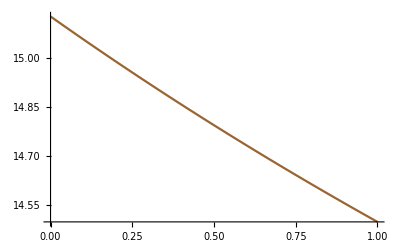

```mathematica
(*a2*)
Clear[a2]
a0=a;a1=a;a3=a;a4=a;
pltV1a2 = Plot[V[[1]],{a2,0,1},PlotStyle->Red];
pltV2a2 = Plot[V[[2]],{a2,0,1},PlotStyle->Green];
pltV3a2 = Plot[V[[3]],{a2,0,1},PlotStyle->Blue];
pltV4a2 = Plot[V[[4]],{a2,0,1},PlotStyle->Black];
pltV5a2 = Plot[V[[5]],{a2,0,1},PlotStyle->Yellow];
pltVsum = Plot[Total[V],{a2,0,1},PlotStyle->Brown];
Show[pltVsum,PlotRange->All]
```

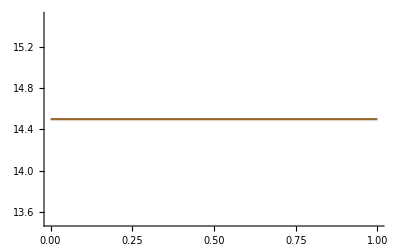

```mathematica
(*a3*)
Clear[a3]
(*a0=0.7;a1=0.38;a2=0.48;a4=0.994;*)
a0=a;a1=a;a2=a;a4=a;
pltV1a3 = Plot[V[[1]],{a3,0,1},PlotStyle->Red];
pltV2a3 = Plot[V[[2]],{a3,0,1},PlotStyle->Green];
pltV3a3 = Plot[V[[3]],{a3,0,1},PlotStyle->Blue];
pltV4a3 = Plot[V[[4]],{a3,0,1},PlotStyle->Black];
pltV5a3 = Plot[V[[5]],{a3,0,1},PlotStyle->Yellow];
pltVsum = Plot[Total[V],{a3,0,1},PlotStyle->Brown];
Show[pltVsum,PlotRange->All]
(*Show[pltV1a3,pltV2a3,pltV3a3,pltV4a3,pltV5a3,pltVsum,PlotRange->All]*)
```

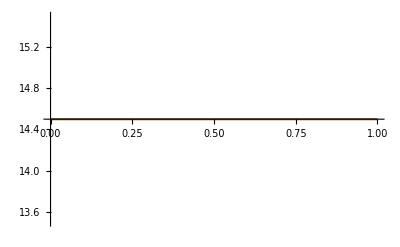

```mathematica
(*a3*)
Clear[a4]
a0=a;a1=a;a2=a;a3=a;
pltV1a4 = Plot[V[[1]],{a4,0,1},PlotStyle->Red];
pltV2a4 = Plot[V[[2]],{a4,0,1},PlotStyle->Green];
pltV3a4 = Plot[V[[3]],{a4,0,1},PlotStyle->Blue];
pltV4a4 = Plot[V[[4]],{a4,0,1},PlotStyle->Black];
pltV5a4 = Plot[V[[5]],{a4,0,1},PlotStyle->Yellow];
pltVsum = Plot[Total[V],{a4,0,1},PlotStyle->Brown];
Show[pltVsum,PlotRange->All]
```

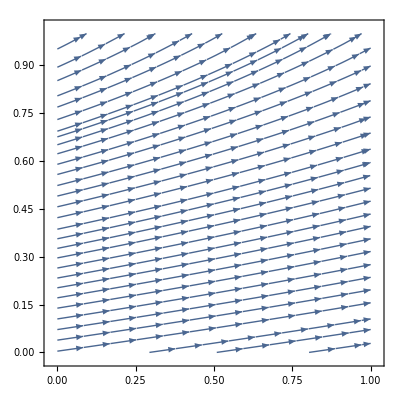

```mathematica
(*a0 v. a3 ------------------------------------------------------------------------------------------------------------------------------------*)
(*Initial: All-coop, versus Tit-for-Tat*)
Clear[a3,a4];
R=3;S=0;T=5;P=1;
a=1;
gamma=0.78;
a3=a;a4=a;a2=a;
(*a1=0.38;a2=0.48;a4=0.994;*)
b0=1; b1=1;b2=1;b3=0;b4=0;
b0=0; b1=9/13;b2=7/13;b3=0;b4=0;
Clear[a0,a1]
V0 = D[Total[V],a0];
V1 = D[Total[V],a1];
StreamPlot[{V0,V1},{a0,0,1},{a1,0,1}]
```

```mathematica
V1
```

-4/(27 (4/9+(2 a4)/9)^2)-(2 (2/9-(2 a3)/9))/(9 (4/9+(2 a4)/9)^2)-(38 (1+1/3 (-1+a4)))/(27 (4/9+(2 a4)/9)^2)-(2 ((2 a3)/27+a4/27))/(3 (4/9+(2 a4)/9)^2)-(4 (2/9+a4/9))/(3 (4/9+(2 a4)/9)^2)+29/(9 (4/9+(2 a4)/9))-(2 a4)/(27 (4/9+(2 a4)/9)^2)

```mathematica
Clear[a1,a2,a3];
R=3;S=0;T=5;P=1;
a=0.99;
gamma=2/3;
a0=a;a4=a;
amin = 0;
amax = 1;
(*a1=0.38;a2=0.48;a4=0.994;*)
b0=1; b1=1;b2=1;b3=0;b4=0;
V0 = D[Total[V],a1];
V1 = D[Total[V],a2];
V2 = D[Total[V],a3];
VectorPlot3D[{V0,V1,V2},{a1,amin,amax},{a2,amin,amax},{a3,amin,amax}]
```

-Graphics3D-

```mathematica
(*V1(a0) ---------------------------------------------------------------------------------------------------------------------------------------*)
```

4/7

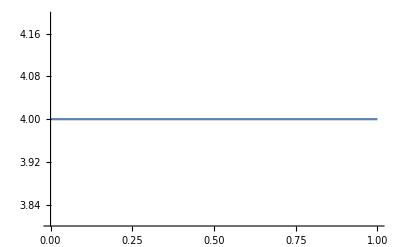

{4.+4.44089×10^-16 a0,7.,4.,7.,3.}

```mathematica
(*Initial: random, versus Tit-for-Tat*)
R=3;S=0;T=5;P=1;
a1=0.5;a2=0.5;a3=0.5;a4=0.5;
b0=1; b1=1;b2=1;b3=0;b4=0;
gamma=4/7
Plot[V[[1]],{a0,0,1}]
Simplify[V]
```

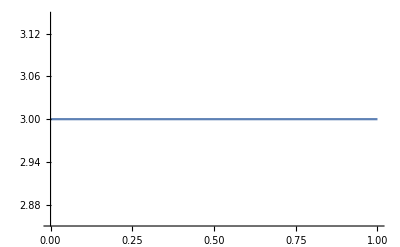

{3,6,3,6,2}

```mathematica
(*Initial: all-defect, versus Tit-for-Tat*)
R=3;S=0;T=5;P=1;
a1=0;a2=0;a3=0;a4=0;
b0=1; b1=1;b2=1;b3=0;b4=0;
gamma=1/2;
Plot[V[[1]],{a0,0,1}]
Simplify[V]
```

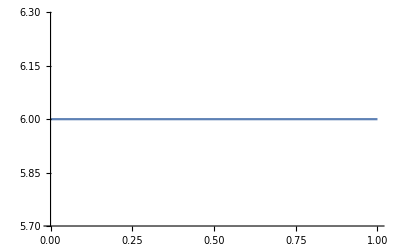

{6,9,6,9,5}

```mathematica
(*Initial: all-coop, versus Tit-for-Tat*)
R=3;S=0;T=5;P=1;
a1=1;a2=1;a3=1;a4=1;
b0=1; b1=1;b2=1;b3=0;b4=0;
gamma=2/3;
Plot[V[[1]],{a0,0,1}]
Simplify[V]
```

```mathematica
(*Initial: random, versus win-stay-lose-shift (Pavlov)*)
R=3;S=0;T=5;P=1;
a1=0.5;a2=0.5;a3=0.5;a4=0.5;
b0=1; b1=1;b2=0;b3=0;b4=1;
gamma=4/7;
Plot[V[[1]],{a0,0,1}]
Simplify[V]
```

-Graphics-

{4.-1.33227×10^-15 a0,7.,2.,7.,5.}

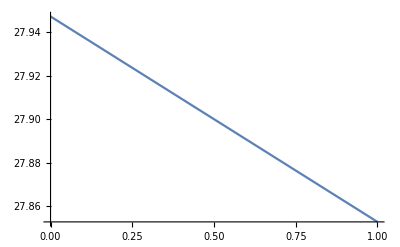

{27.9474-0.0947368 a0,30.9474,26.0526,31.0526,28.9474}

```mathematica
(*Initial: all-defect, versus win-stay-lose-shift (Pavlov)*)
R=3;S=0;T=5;P=1;
a1=0;a2=0;a3=0;a4=0;
b0=1; b1=1;b2=0;b3=0;b4=1;
gamma=0.9;
Plot[V[[1]],{a0,0,1}]
Simplify[V]
```

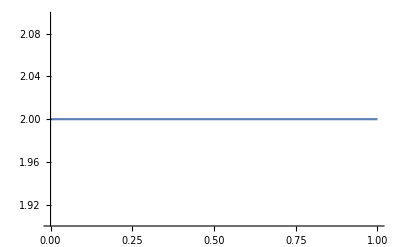

{2,5,0,5,3}

```mathematica
(*Initial: all-coop, versus win-stay-lose-shift (Pavlov)*)
R=3;S=0;T=5;P=1;
a1=1;a2=1;a3=1;a4=1;
b0=1; b1=1;b2=0;b3=0;b4=1;
gamma=2/5;
Plot[V[[1]],{a0,0,1}]
Simplify[V]
```